```mathematica
kpcSI=3.08567758*10^(19) (*[m]*)
MsolarSI=1.98847*10^(30) (*[kg]*)
rhos = 17200000.0 (*[M_solar/kpc^3]*)
rs = 6.32 (*[kpc]*)
constG = 6.67*10^(-11) * (1/MsolarSI)^(-1)*(1/kpcSI)^(2)
rhosSI = 17200000.0  * MsolarSI * kpcSI^(-3)(*[kg/m^3]*)
rsSI = 6.32 *kpcSI(*[m]*)
constGSI = 6.67*10^(-11)(*[m/s^2 * kg-1 * m^2]*)
Subscript[ρ, NFW][r_]:= Subscript[ρ, s]/(r/Subscript[R, s](1+r/Subscript[R, s])^2)
Subscript[f, NFW][x_]:=Log[1+x]-x/(1+x)
Subscript[M, NFW][r_]:=4π Subscript[ρ, s] Subscript[R, s]^3*Subscript[f, NFW][r/Subscript[R, s]]
```

3.08568×10^19

1.98847×10^30

1.72×10^7

6.32

1.39298×10^-19

1.16411×10^-21

1.95015×10^20

6.67×10^-11

```mathematica
DSolve[ν2'[r]== -G (Subscript[M, NFW][r])/r^2-(Subscript[ρ, NFW]'[r])/(Subscript[ρ, NFW][r])ν2[r],ν2[r],r]
```

{{ν2[r]→r C[1] (r+R_s)^2-4 G π r R_s^3 (r+R_s)^2 ((3 Log[r])/R_s^4-(3 Log[1+r/R_s]^2)/(2 R_s^4)-(3 Log[r+R_s])/R_s^4-(3 PolyLog[2,-r/R_s])/R_s^4+1/(r R_s^3)-(2 (-Log[1+r/R_s]/r+Log[r]/R_s-Log[r+R_s]/R_s))/R_s^3+1/(2 R_s^2 (r+R_s)^2)+2/(R_s^3 (r+R_s))+(1+Log[1+r/R_s])/(R_s^3 (r+R_s))-(r^2 (Log[r]-Log[r+R_s])+r R_s+Log[1+r/R_s] R_s^2)/(2 r^2 R_s^4)) ρ_s}}

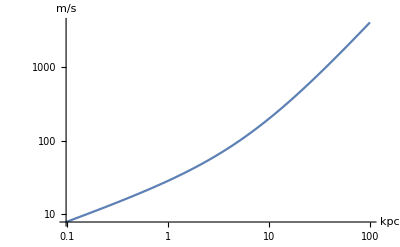

```mathematica
LogLogPlot[((r) C[1] (r+Subscript[R, s])^2-4 G π (r) Subscript[R, s]^3 (r+Subscript[R, s])^2 ((3 Log[r])/Subscript[R, s]^4-(3 Log[1+r/Subscript[R, s]]^2)/(2 Subscript[R, s]^4)-(3 Log[r+Subscript[R, s]])/Subscript[R, s]^4-(3 PolyLog[2,-r/Subscript[R, s]])/Subscript[R, s]^4+1/(r Subscript[R, s]^3)-(2 (-Log[1+r/Subscript[R, s]]/r+Log[r]/Subscript[R, s]-Log[r+Subscript[R, s]]/Subscript[R, s]))/Subscript[R, s]^3+1/(2 Subscript[R, s]^2 (r+Subscript[R, s])^2)+2/(Subscript[R, s]^3 (r+Subscript[R, s]))+(1+Log[1+r/Subscript[R, s]])/(Subscript[R, s]^3 (r+Subscript[R, s]))-((r)^2 (Log[r]-Log[r+Subscript[R, s]])+r Subscript[R, s]+Log[1+r/Subscript[R, s]] Subscript[R, s]^2)/(2 (r)^2 Subscript[R, s]^4)) Subscript[ρ, s])^(1/2)/.{Subscript[ρ, s]->rhos, Subscript[R, s]->rs, G->constG, C[1] ->15},{r,0, 100}, AxesLabel->{kpc, m/s}]
```